```mathematica
releventCA={30,45,73,110,150,105,54,22,60,146,126,62,90,18,122,26,154,94,41,57,156,28,58,78,178,77,50,13,25,37,9,35,106,3,27,43,184,56,11,142,14,134,24,7,152,170,46,15,33,1,42,162,6,5,138,38,10,74,34,29,130,2,204,200,172,108,76,72,51,44,104,232,140,132,23,12,164,36,19,4,168,40,160,136,128,32,8,0};
rulecombinations=Sort/@Tuples[releventCA,2]//DeleteDuplicates;
rulecombinations//Length
```

3916

```mathematica
in=Join[Table[Import["Research Projects/GRs/GR Plot Stuff/gr_"<>ToString[i]<>"Plot.csv"]//ToExpression,{i,1,633}],Table[Import["Research Projects/GRs/GR Plot Stuff/gr_"<>ToString[i]<>"Plot.csv"]//ToExpression,{i,700,799}]];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

```mathematica
in2=DeleteCases[Table[If[Length[in[[i]]]==100,in[[i]]],{i,1,Length[in]}],Null];
```

```mathematica
in3=Table[If[((Total/@in2)[[i]]//Length)==5,Drop[(Total/@in2)[[i]],-1],(Total/@in2)[[i]]],{i,1,Length[(Total/@in2)]}];
```

```mathematica
in4=in3//Total;
```

```mathematica
hists=Table[
Table[
Table[in4[[i]][[k]][[j]],{i,1,4}]
,{j,1,4}]
,{k,1,4}];
```

```mathematica
f[x_]:=Normalize[x,Max]
g[x_]:=BarChart[x,ChartStyle->24,ImageSize->Small,AspectRatio->1/2]
Table[Export["gr_hist_"<>ToString[l]<>".pdf",(g/@f/@Flatten[hists,1])[[l]]],{l,1,16}]
```

{gr_hist_1.pdf,gr_hist_2.pdf,gr_hist_3.pdf,gr_hist_4.pdf,gr_hist_5.pdf,gr_hist_6.pdf,gr_hist_7.pdf,gr_hist_8.pdf,gr_hist_9.pdf,gr_hist_10.pdf,gr_hist_11.pdf,gr_hist_12.pdf,gr_hist_13.pdf,gr_hist_14.pdf,gr_hist_15.pdf,gr_hist_16.pdf}

```mathematica
in2=Flatten[Table[Table[in[[j]][[i]][[1;;4]],{i,1,Length[in[[j]]]}],{j,1,Length[in]}],1];
```

```mathematica
in3=Table[
Table[
Table[
in2[[k]][[j]][[i]][[1;;4]]
,{i,1,Length[in2[[k]][[j]]]}]
,{j,1,Length[in2[[k]]]}]
,{k,1,Length[in2]}];
```

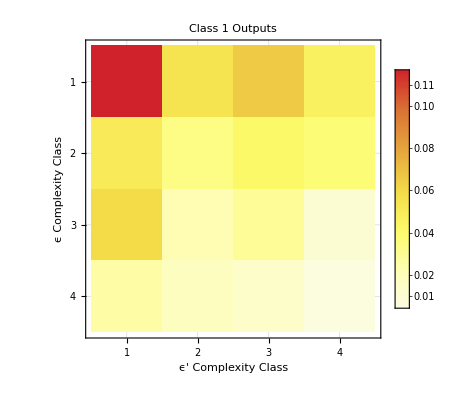
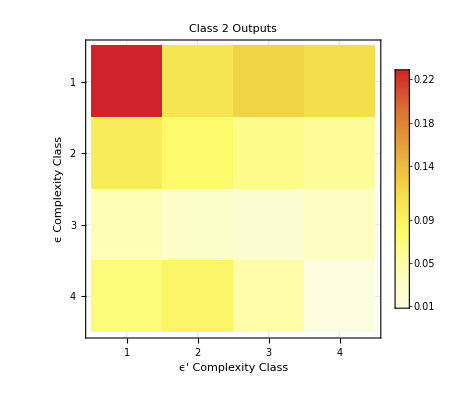
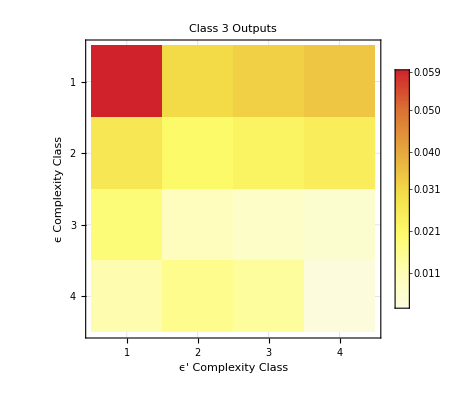
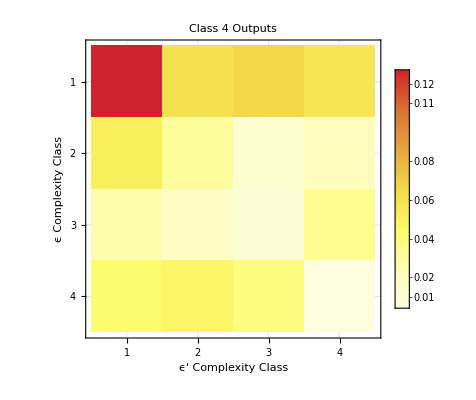

```mathematica
f[x_]:=MatrixPlot[x,FrameLabel->{"ϵ Complexity Class","ϵ' Complexity Class"},FrameTicks->{{All,None},{All,None}},PlotLabel->"Class "<>ToString[i]<>" Outputs",PlotLegends->Automatic,PlotTheme->"Business",ColorFunction->"Temperature"]
Table[((in3//Total)/1666251749)[[i]]//f,{i,1,4}]
```

```mathematica
Export["preplots.pdf",plots]
```

preplots.pdf

```mathematica
Length[in3]
```

425600

```mathematica
Export["GRData.csv",in3]
```

GRData.csv

```mathematica
rawindex=Append[Drop[Import["GRindex.csv"]//ToExpression//Flatten//Sort,-1],5315];
index=Table[Table[i,{i,rawindex[[j]]*100-100+1,rawindex[[j]]*100}],{j,1,Length[rawindex]}]//Flatten;
```

```mathematica
f[x_]:=x[[4]]
Position[f/@in3,2211]
```

{{32685,1,1},{36983,1,1},{40921,1,1},{72399,1,1}}

```mathematica
in3[[77399]]
```

{{{17,34,15,0},{84,185,95,44},{8,22,12,5},{2,15,9,25}},{{3,8,3,0},{24,43,14,30},{8,1,2,0},{5,4,4,0}},{{2211,0,0,0},{22,25,6,184},{112,75,110,21},{2,13,3,1}},{{32,29,18,212},{9,5,1,21},{5,22,12,1},{4,1,1,0}}}

GRs of interest: from in3, 
77399 highest number of class3 from  1-1
72399, 40921, 36983, 32685 highest number of class4 from  1-1
77399, 72399, 40921, 36983, 32685

```mathematica
index[[{77399,72399,40921,36983,32685}]]
```

```mathematica
{77499,72499,40921,36983,32685}
{77499,72499,40921,36983,32685}
```

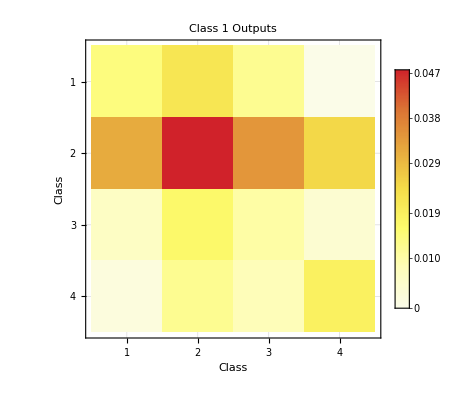
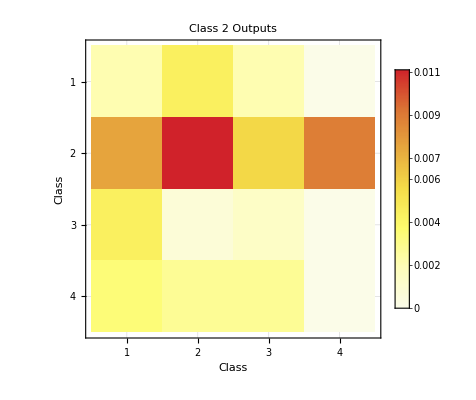
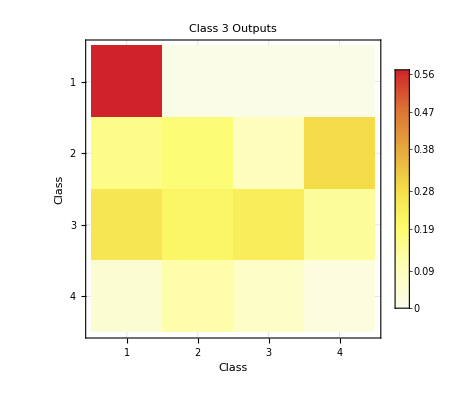
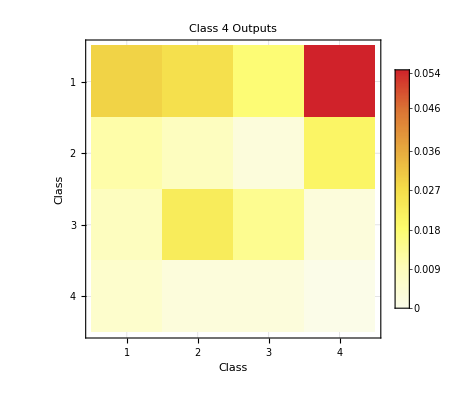
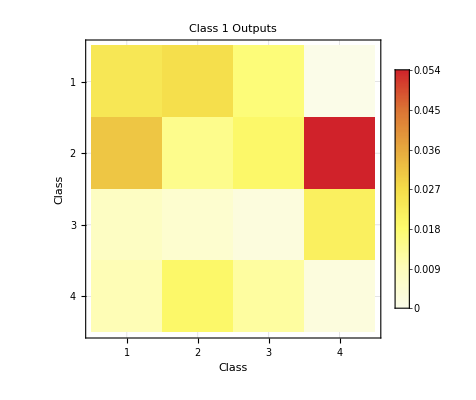
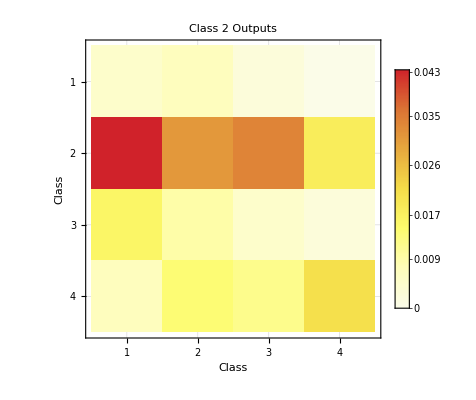
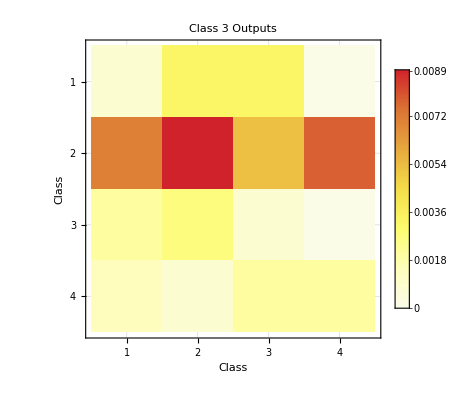
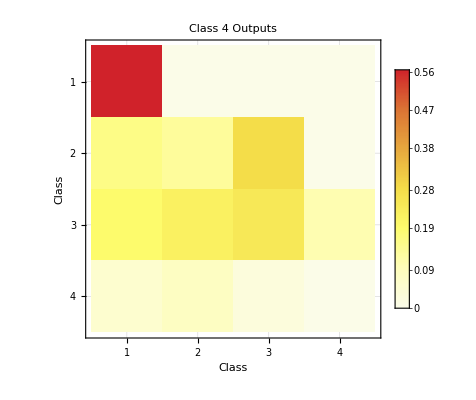
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Table[
f[x_]:=MatrixPlot[x,FrameLabel->{"Class","Class"},FrameTicks->{{All,None},{All,None}},PlotLabel->"Class "<>ToString[i]<>" Outputs",PlotLegends->Automatic,PlotTheme->"Business",ColorFunction->"Temperature"];
plot=Grid[{Table[(in3[[j]]/(in3[[j]]//Flatten//Total))[[i]]//f,{i,1,4}]}]
,{j,{77399,72399,40921,36983,32685}}]//Column
```

```mathematica
Table[
f[x_]:=MatrixPlot[x,FrameLabel->{"Class","Class"},FrameTicks->{{All,None},{All,None}},PlotLabel->"Class "<>ToString[i]<>" Outputs",PlotLegends->Automatic,PlotTheme->"Business",ColorFunction->"Temperature"];
plot=Grid[{Table[(in3[[j]]/(in3[[j]]//Flatten//Total))[[i]]//f,{i,1,4}]}];
Export["GR-Output-Plots/GR_Outputs_"<>ToString[index[[j]]]<>".png",plot]
,{j,1,Length[index]}];
```

Part::take: Cannot take positions 2 through -2 in {0.}.

Join::heads: Heads Part and List at positions 1 and 3 are expected to be the same.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

Part::take: Cannot take positions 2 through -2 in {0.}.

General::stop: Further output of Part :: take will be suppressed during this calculation.

Join::heads: Heads Part and List at positions 1 and 3 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

Export::noopen: Cannot open "/Users/alyssa/GR-Output-Plots/GR_Outputs_10362.png".

Export::nodir: Directory "/Users/alyssa/GR-Output-Plots/" does not exist.

Export::noopen: Cannot open "GR-Output-Plots/GR_Outputs_10363.png".

Export::nodir: Directory "/Users/alyssa/GR-Output-Plots/" does not exist.

Export::noopen: Cannot open "GR-Output-Plots/GR_Outputs_10364.png".

General::stop: Further output of Export :: noopen will be suppressed during this calculation.

Export::nodir: Directory "/Users/alyssa/GR-Output-Plots/" does not exist.

General::stop: Further output of Export :: nodir will be suppressed during this calculation.

$Aborted

```mathematica
index//Length
```

425600